```mathematica
MaxRodStates[n_]:=4+2^(n-2)+4

ToRodRule[rule_]:=Join[MapThread[Rule,{Join[Prepend[2]/@Tuples[{0,1},2],Tuples[{0,1},3],Append[2]/@Tuples[{0,1},2]],IntegerDigits[rule-1,2,16]}],{{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2}]

RodEvolution[rule_,n_,t_,init_:Automatic]:=CellularAutomaton[ToRodRule[rule],Replace[init,Automatic->Join[{2},ConstantArray[0,n],{2}]],t]
```

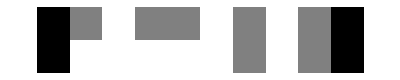

```mathematica
n=10;
start =RandomChoice[{0,1},n-2];
step1 = RodEvolution[50845,n,1,Join[{2},start,{2}]];
ArrayPlot[step1]
```

```mathematica
IntegerDigits[50-1,2,16]
```

{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1}